```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m
```

∀_x∃_y x⊗y≻y&&m≠0⇒n⧐̸m

```mathematica
FullForm[%]
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
a*a*a*b*b*c
```

a^3 b^2 c

```mathematica
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
∫a[x] b[x] ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
x^(a+b)
```

x^(a+b)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
∑_(n=1)^∞ 1/n^s + n
```

n+Zeta[s]

```mathematica
Expand[(x+1)^2]
```

1+2 x+x^2

```mathematica
1+2/3
```

5/3

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,1,{3,4,5},{3,2}}
```

{1,1,{3,4,5},{3,2}}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
v=Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

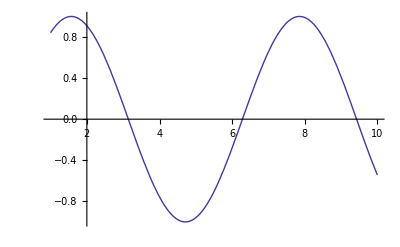

```mathematica
Plot[Sin[x],{x,1,10}]
```

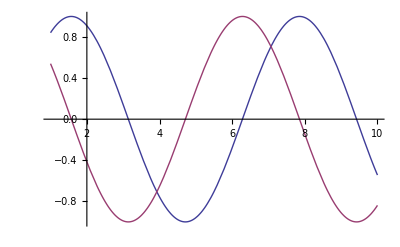

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
3+62-1
```

64

```mathematica
3 x-x+2
```

2+2 x

```mathematica
-1+2 x+x^3
```

-1+2 x+x^3

```mathematica
x^2+x-4 x^2
```

x-3 x^2

```mathematica
x y+2 x^2 y+y^2 x^2-2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(x+2 y+1) (x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
(x+2 y+1) (x-2)^2;
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
Log[1+Cos[x]]
```

Log[1+Cos[x]]

```mathematica
1+2 x/.x->3
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
x->3+y
```

x→3+y

```mathematica
x^2-9/.%
```

-9+(3+y)^2

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

```mathematica
x=3
```

3

```mathematica
x^2-1
```

8

```mathematica
x=1+a
```

1+a

```mathematica
x^2-1
```

-1+(1+a)^2

```mathematica
x+5-2 x
```

6+a-2 (1+a)

```mathematica
x=.
```

```mathematica
x+5-2 x
```

5-x

```mathematica
t=1+x^2
```

1+x^2

```mathematica
t/.x->2
```

5

```mathematica
t/.x->5 a
```

1+25 a^2

```mathematica
t/.x->Pi//N
```

10.8696

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[%]
```

(1+x+3 y)^4

```mathematica
Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Expand[%]
```

-1+x^10

```mathematica
Simplify[x^2+2 x+1]
```

(1+x)^2

```mathematica
Simplify[x^10-1]
```

-1+x^10

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Simplify[Gamma[x] Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x] Gamma[1-x]]
```

π Csc[π x]